# wbBrancUniBFBcheck

function that gives the couplings according to the UNI and BFB conditions of Branco's model.

## Documentation

### Usage

wbBrancUniBFBcheck[mode, options]
wbBrancUniBFBcheck[list, mode, options]

Generate and filter the couplings according to the UNI and BFB conditions using the methods and accuracy prescriptions described in Ref. [1]. Return the list of generated (initial) points and the list of validated points.

### Details & Options

Four accuracy modes are available for BFB filtering:
for mode = 0, the sufficient BFB conditions are imposed using the function wbBrancSufCond
for mode = 1, the necessary 2HDM BFB conditions (NCL1) are imposed using the function wbBrancNecCond1
for mode = 2, the additional necessary BFB conditions (NCL1-NCL3) are imposed using the function wbBrancNecCond2
for mode = 3, the additional necessary BFB conditions (NCL1-NCL4) are imposed using the function wbBrancNecCond3
for mode = 4, the quartic potential is minimized using the function wbMinimFuncPotBranc

An initial data set satisfying only the UNI conditions, only the necessary 2HDM BFB conditions (NCL1), or both can be generated by selecting the appropriate options. The initial data set can also be imported via the global parameter “wbParamData” or passed directly to wbBrancUniBFBcheck as a list.

An initial data set satisfying the UNI and BFB conditions can be generated using neural networks by setting the option "NeuralNets"→True.

The following options can be given:

Option | Default value | Meaning
GeneratePoints | True | generation of the initial dataset
ImposeUNI | True | filter the couplings according to the UNI conditions
ImposeBFB | True | filter the couplings according to the BFB conditions
NeuralNets | False | neural networks are used
ExportData | False | the initial and validated data sets are exported to a file
ShowMessages | True | messages reporting the computation times and results are displayed
NPoints | 10^3 | number of initial points in the dataset
MaxCoupling | 16 | bounds for the generated couplings
BoundUNI | 8π | unitarity bound
FileNameInit | initial_set.csv | file name for initial dataset
FileNameValid | valid_set.csv | file name for validated dataset

## Examples

To test usage examples make sure the package has been loaded:

```mathematica
wbLoadBinaries=True; (*wpCompTarget="C";*)
NotebookEvaluate[FileNameJoin[{ParentDirectory@NotebookDirectory[EvaluationNotebook[]],"StableWein.nb"}]]
```

### Basic Examples

The options for wbWeinUniBFBcheck can be set manually:

```mathematica
wbGeneratePoints=True;
wbImposeUNI=True;
wbImposeBFB=True;
wbNeuralNets=False;
wbExportData=False;
wbShowMessages=True;

wbNPoints=1*10^4;
wbMaxCoupling=16;
wbBoundUNI=8*Pi;

wbFileNameInit="initial_set.csv";
wbFileNameValid="valid_set.csv";

wbBrancOpts=Thread[Options[wbBrancUniBFBcheck][[;;,1]]->{wbGeneratePoints,wbImposeUNI,wbImposeBFB,wbNeuralNets,wbExportData,wbShowMessages,wbNPoints,wbMaxCoupling,wbBoundUNI,wbFileNameInit,wbFileNameValid}];
```

Generation of 10^4 points which satisfy only UNI conditions:

```mathematica
{initParamSet,dataUNI}=wbBrancUniBFBcheck[3,"NPoints"->10^4,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.341103 sec.

In this case, the generated and validated data sets are identical:

```mathematica
initParamSet==dataUNI
```

True

Generation of 10^4 points which satisfy UNI conditions and then filtering according BFB conditions with mode = 3:

```mathematica
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,wbBrancOpts];
```

Run time of data generation (UNI+Nec1): 3.67967 sec.

Run time of the BFB enforcement (mode 3): 0.520086 sec.

BFB points: 7532

Fractions of points satisfying the BFB conditions:

```mathematica
{initParamSet,dataNec1}=wbBrancUniBFBcheck[1,"ShowMessages"->False];
wbParamData=initParamSet;
{initParamSet,dataSuf}=wbBrancUniBFBcheck[0,"GeneratePoints"->False,"ShowMessages"->False];
{initParamSet,dataNec2}=wbBrancUniBFBcheck[2,"GeneratePoints"->False,"ShowMessages"->False];
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,"GeneratePoints"->False,"ShowMessages"->False];
Length/@{dataNec1,dataSuf,dataNec2,dataNec3}
PercentForm/@N[%/Length[wbParamData]]
```

{1000,587,745,745}

{100%,58.7%,74.5%,74.5%}

### Scope

Couplings are generated in the range ∣coupling∣ ≤ 10 and are then filtered to retain only those that satisfy the relevant BFB conditions.

```mathematica
optTMP=wbOptChange[wbBrancOpts,{"GeneratePoints","ImposeUNI"},{False,False}];
```

```mathematica
{initParamSet,dataNec1}=wbBrancUniBFBcheck[1,"NPoints"->10^6,"MaxCoupling"->10,"ImposeUNI"->False];
wbParamData=dataNec1;
{initParamSet,dataNec2}=wbBrancUniBFBcheck[2,optTMP];
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,optTMP];
Length/@{dataNec1,dataNec2,dataNec3}
PercentForm/@N[%/Length[wbParamData]]
```

Run time of data generation (NCL1): 1.53651 sec.

BFB points: 1000000

Run time of the BFB enforcement (mode 2): 12.028 sec.

BFB points: 942577

Run time of the BFB enforcement (mode 3): 22.6825 sec.

BFB points: 942557

{1000000,942577,942557}

{100%,94.26%,94.26%}

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataNec3),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"mode = 1","mode = 2","mode = 3"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

mode = 1
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.86 | 10.
b_2 | -9.76 | 10.
b_3 | -9.83 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10. | mode = 2
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.86 | 10.
b_2 | -9.7 | 10.
b_3 | -9.79 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10. | mode = 3
 | Min | Max
a_1 | 0. | 10.
a_2 | 0. | 10.
a_3 | 0. | 10.
b_1 | -9.86 | 10.
b_2 | -9.7 | 10.
b_3 | -9.79 | 10.
c_1 | -10. | 10.
c_2 | -10. | 10.
c_3 | -10. | 10.
d_1 | -10. | 10.
d_2 | -10. | 10.
d_3 | -10. | 10.

Distribution of the couplings filtered using mode = 1 (green contour), mode = 2 (blue dashed contour), and mode = 3 (red dashed contour):

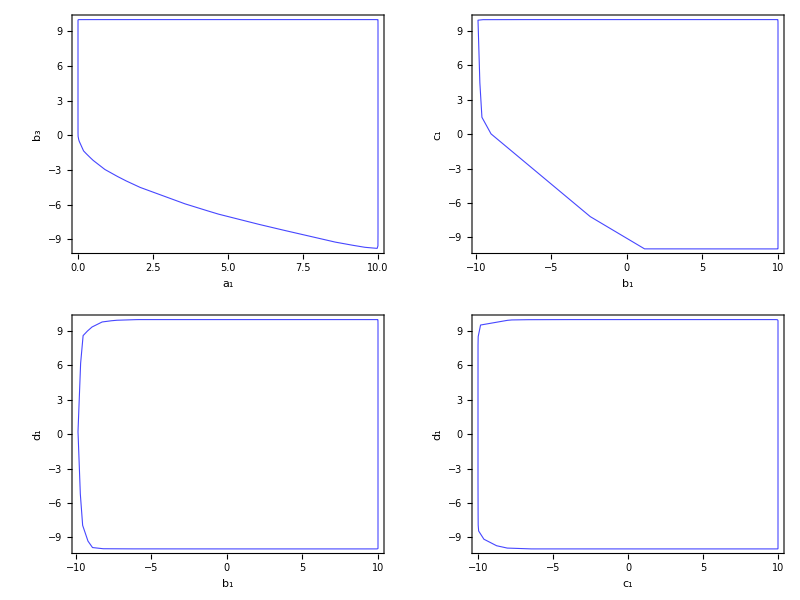

```mathematica
Table[Show[{ConvexHullMesh[dataNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataNec2[[;;,xx]],MeshCellStyle->{1->{Lighter[Blue,0.2],Dashing[{0.09,0.03}],Opacity[0.9]},2->Opacity[0,Blue]}],ConvexHullMesh[dataNec3[[;;,xx]],MeshCellStyle->{1->{Red,Dashing[{0.01,0.01}]},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]},Epilog->{Inset[(*Framed[#,Background->White,FrameStyle->Black,RoundingRadius->10]&@*)Graphics[makePlotLegend[{"mode 1","mode 2","mode 3"},{Graphics[{Thickness[0.04],Darker[Green,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.45,0.08}],Lighter[Blue,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.1,0.1}],Red,Line[{{-1,0},{0,0}}]}]},{-0.08,1.1},30,12,FontFamily->"Times"],PlotRange->{{0,0.08},{0,0.04}},ImageSize->80],Scaled[{0.27,0.83}]]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

Couplings are generated to satisfy the UNI and NCL1 conditions, and are then filtered to retain only those that also satisfy the NCL2-NCL3 or NCL4 BFB conditions:

```mathematica
optTMP=wbOptChange[Options[wbBrancUniBFBcheck],{"GeneratePoints","ImposeUNI"},{False,False}];
```

```mathematica
{initParamSet,dataUniNec1}=wbBrancUniBFBcheck[1,"NPoints"->10^6];
wbParamData=dataUniNec1;
{initParamSet,dataUniNec2}=wbBrancUniBFBcheck[2,optTMP];
{initParamSet,dataUniNec3}=wbBrancUniBFBcheck[3,optTMP];
Length/@{dataUniNec1,dataUniNec2,dataUniNec3}
PercentForm/@N[%/Length[wbParamData]]
```

Run time of data generation (UNI+NCL1): 376.484 sec.

BFB points: 1000000

Run time of the BFB enforcement (mode 2): 17.2486 sec.

BFB points: 751069

Run time of the BFB enforcement (mode 3): 40.1699 sec.

BFB points: 750988

{1000000,751069,750988}

{100%,75.11%,75.1%}

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3"};
table1=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec1),TableHeadings->{parNames,{"Min","Max"}}]; 
table2=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec2),TableHeadings->{parNames,{"Min","Max"}}]; 
table3=TableForm[Round[#,10.^-2]&/@(MinMax/@Transpose@dataUniNec3),TableHeadings->{parNames,{"Min","Max"}}];
Grid[#,Spacings->{0, 1}]&/@(Partition[#,1]&/@Transpose[{{"mode = 1","mode = 2","mode = 3"},{table1,table2,table3}}]);
Grid[{%},Spacings->{4, 0}]
```

mode = 1
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.38
a_3 | 0. | 8.38
b_1 | -7.6 | 15.78
b_2 | -7.88 | 15.82
b_3 | -7.63 | 15.69
c_1 | -15.76 | 15.96
c_2 | -15.97 | 16.03
c_3 | -15.61 | 15.83
d_1 | -8.16 | 8.19
d_2 | -8.17 | 8.14
d_3 | -8.17 | 8.16 | mode = 2
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.38
a_3 | 0. | 8.38
b_1 | -7.31 | 15.78
b_2 | -7.5 | 15.82
b_3 | -7.5 | 15.69
c_1 | -15.76 | 14.94
c_2 | -14.95 | 15.34
c_3 | -15.61 | 15.52
d_1 | -8.1 | 8.07
d_2 | -7.94 | 8.08
d_3 | -7.91 | 7.97 | mode = 3
 | Min | Max
a_1 | 0. | 8.37
a_2 | 0. | 8.38
a_3 | 0. | 8.38
b_1 | -7.31 | 15.78
b_2 | -7.5 | 15.82
b_3 | -7.5 | 15.69
c_1 | -15.76 | 14.94
c_2 | -14.95 | 15.34
c_3 | -15.61 | 15.52
d_1 | -8.1 | 8.07
d_2 | -7.94 | 8.08
d_3 | -7.91 | 7.97

Distribution of the couplings satisfying UNI conditions and filtered using mode = 1 (green contour), mode = 2 (blue dashed contour), and mode = 3 (red dashed contour):

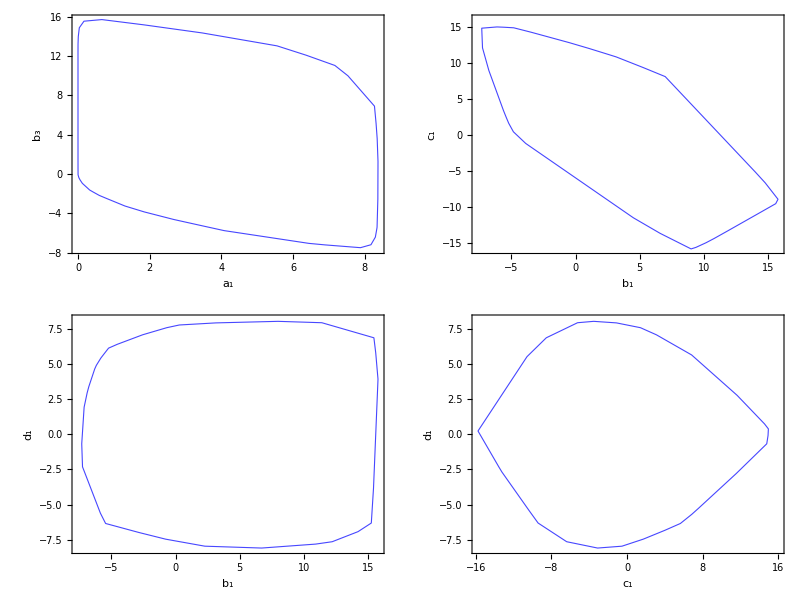

```mathematica
Table[Show[{ConvexHullMesh[dataUniNec1[[;;,xx]],MeshCellStyle->{1->{Darker[Green,0.2]},2->Opacity[0,Green]}],ConvexHullMesh[dataUniNec2[[;;,xx]],MeshCellStyle->{1->{Lighter[Blue,0.2],Dashing[{0.09,0.03}],Opacity[0.9]},2->Opacity[0,Blue]}],ConvexHullMesh[dataUniNec3[[;;,xx]],MeshCellStyle->{1->{Red,Dashing[{0.01,0.01}]},2->Opacity[0,Red]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->250,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]},Epilog->{Inset[(*Framed[#,Background->White,FrameStyle->Black,RoundingRadius->10]&@*)Graphics[makePlotLegend[{"mode 1","mode 2","mode 3"},{Graphics[{Thickness[0.04],Darker[Green,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.45,0.08}],Lighter[Blue,0.2],Line[{{-1,0},{0,0}}]}],Graphics[{Thickness[0.04],Dashing[{0.1,0.1}],Red,Line[{{-1,0},{0,0}}]}]},{-0.08,1.1},30,12,FontFamily->"Times"],PlotRange->{{0,0.08},{0,0.04}},ImageSize->80],Scaled[{0.35,0.65}]]}],{xx,{{1,6},{4,7},{4,10},{7,10}}}];
Grid[Partition[%,2]]
```

To improve the accuracy of the scan over the orbit-space surface (function wbBrancNecCond3), the scanning grid can be refined by adjusting the parameter values of stepsWein. Note that increasing these values also increases the computation time. For most practical applications (≈99.99% accuracy), the default settings (stepsBranc = {17, 15}) are sufficient; however, to achieve near-100% accuracy it may be necessary to increase them, for example to stepsWein = {50, 80}.

By default, the global parameters (wbfaceListBranc and  wbθListBranc) specify the following numbers of grid points:

```mathematica
Length/@{wbfaceListBranc,wbθListBranc}
```

{5148,4417}

which enables relatively fast filtering of BFB-allowed points:

```mathematica
wbParamData=ParallelTable[wbBrancParRndNec[10],{10^6}];
```

```mathematica
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,"GeneratePoints"->False,"ImposeUNI"->False];
```

Run time of the BFB enforcement (mode 3): 24.4923 sec.

BFB points: 87513

Using wbBrancGridGen, we increase the number of grid points:

```mathematica
stepsBranc={50,50};
{wbfaceListBranc,wbθListBranc}=wbBrancGridGen[stepsBranc];
```

Number of points in Branco's grids: {125504, 145561}

which allows BFB-allowed points to be filtered more accurately, at the cost of increased computational time:

```mathematica
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,"GeneratePoints"->False,"ImposeUNI"->False];
```

Run time of the BFB enforcement (mode 3): 35.7206 sec.

BFB points: 87513

Note that wbBrancUniBFBcheck with mode = 3 yields highly accurate results even with the default grids because it operates in combination with wbBrancSufCond and wbBrancNecCond2.

The default grid points wbfaceListBranc on the surface of the phase space:

```mathematica
labels=Style[#,Black,13]&/@{"P_1","P_2","P_3","P_4"};
pointPos={{1,0,0},{0,1,0},{0,0,1},{1,1,1}};
labPos={{0.95,0,0},{0,0.95,0},{0,0,1},{1,1,1}};
Show[{Plot3D[{(√(w2*w3)-√((1-w2)*(1-w3)))^2,(√(w2*w3)+√((1-w2)*(1-w3)))^2},{w2,0,1},{w3,0,1},PlotStyle->Directive[Opacity[0.95],Lighter[Blue,0.9],Specularity[White,70]]],ListLinePlot3D[{{0,0,1},{1,1,1},{1,0,0},{0,0,1},{0,1,0},{1,1,1}},PlotRange->All,PlotStyle->{Directive[Darker[Red,0.0],Dashed,Thickness[0.003]]}],ListLinePlot3D[{{0,1,0},{1,0,0}},PlotRange->All,PlotStyle->{Directive[Darker[Red,0.0],Dashed,Thickness[0.003]]}],ListPointPlot3D[wbfaceListBranc,PlotRange->All,AspectRatio->0.9,ImageSize->400,PlotStyle->{Directive[Darker[Blue,0.1],PointSize->0.007]}],ListPointPlot3D[Table[Callout[pointPos[[x]],labels[[x]],labPos[[x]],Appearance->"CurvedLeader"],{x,1,Length[labels]}],PlotStyle->Directive[Black,PointSize->0.009]]},BoxRatios->{1,1,1},PlotRange->{{0,1},{0,1},{0,1}},AspectRatio->0.9,ImageSize->400,PlotStyle->{Directive[Darker[Red,0.1],PointSize->0.007],Directive[Darker[Blue,0.1],PointSize->0.007]},AxesLabel->fLabelSty/@{"ϖ_1","ϖ_2","ϖ_3"}]
```

-Graphics3D-

With mode = 4, the points in the initial data set are validated by minimizing the quartic potential using wbMinimFuncPotBranc. This mode is useful for cross-checking the BFB-validated points obtained with mode = 3 and for achieving maximal accuracy. However, potential minimization is computationally expensive and requires substantial resources:

```mathematica
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,"NPoints"->10^4];
```

Run time of data generation (UNI+Nec1): 3.99269 sec.

Run time of the BFB enforcement (mode 3): 0.386874 sec.

BFB points: 7574

```mathematica
wbParamData=dataNec3;
{initParamSet,validParamSet}=wbBrancUniBFBcheck[4,"GeneratePoints"->False,"ImposeUNI"->False];
```

Run time of the potential minimization (mode 4): 317.464 sec.

BFB points: 7573

Branco’s model (wbBrancUniBFBcheck) is a special case of Weinberg’s model (wbWeinUniBFBcheck) obtained by setting the phase ϵ = 0 (the CP-conserving case):

```mathematica
{initParamSet,dataNec3Branc}=wbBrancUniBFBcheck[3,"NPoints"->10^4];
```

Run time of data generation (UNI+Nec1): 3.6643 sec.

Run time of the BFB enforcement (mode 3): 0.5143 sec.

BFB points: 7414

```mathematica
wbParamData=Join[#,{0}]&/@initParamSet;
```

```mathematica
{initParamSet,dataNec3Wein}=wbWeinUniBFBcheck[3,"GeneratePoints"->False];
```

Run time of the BFB enforcement (mode 3): 3.76659 sec.

BFB points: 7414

```mathematica
dataNec3Branc==dataNec3Wein[[;;,;;-2]]
```

True

Although wbWeinUniBFBcheck produces the same results, wbBrancUniBFBcheck is more optimized for the CP-conserving case, as reflected by the BFB-enforcement runtimes reported above.

### Options

#### Setting options

The default options for wbBrancUniBFBcheck can be modified either directly in the package file “StableWein.nb” or by using SetOptions[wbBrancUniBFBcheck, ...]]:

```mathematica
SetOptions[wbBrancUniBFBcheck,"NPoints"->10^5]
```

{GeneratePoints→True,ImposeUNI→True,ImposeBFB→True,NeuralNets→False,ExportData→False,ShowMessages→True,NPoints→100000,MaxCoupling→16,BoundUNI→8 π,FileNameInit→initial_set.csv,FileNameValid→valid_set.csv}

The option list for wbWeinUniBFBcheck can be created as follows:

```mathematica
wbGeneratePoints=True;
wbImposeUNI=True;
wbImposeBFB=True;
wbNeuralNets=False;
wbExportData=False;
wbShowMessages=True;

wbNPoints=1*10^4;
wbMaxCoupling=16;
wbBoundUNI=8*Pi;

wbFileNameInit="initial_set.csv";
wbFileNameValid="valid_set.csv";

wbBrancOpts=Thread[Options[wbBrancUniBFBcheck][[;;,1]]->{wbGeneratePoints,wbImposeUNI,wbImposeBFB,wbNeuralNets,wbExportData,wbShowMessages,wbNPoints,wbMaxCoupling,wbBoundUNI,wbFileNameInit,wbFileNameValid}];
```

A temporary option list can be created by modifying the default options or a previously defined option list using function wbOptChange:

```mathematica
optTMP=wbOptChange[Options[wbBrancUniBFBcheck],{"GeneratePoints","ImposeUNI"},{False,False}]
```

{GeneratePoints→False,ImposeUNI→False,ImposeBFB→True,NeuralNets→False,ExportData→False,ShowMessages→True,NPoints→100000,MaxCoupling→16,BoundUNI→8 π,FileNameInit→initial_set.csv,FileNameValid→valid_set.csv}

```mathematica
optTMP=wbOptChange[wbBrancOpts,{"ExportData","ImposeBFB","NPoints","MaxCoupling","BoundUNI"},{True,False,10^2,35,16 π}]
```

{GeneratePoints→True,ImposeUNI→True,ImposeBFB→False,NeuralNets→False,ExportData→True,ShowMessages→True,NPoints→100,MaxCoupling→35,BoundUNI→16 π,FileNameInit→initial_set.csv,FileNameValid→valid_set.csv}

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[1,optTMP];
MinMax/@Transpose@initParamSet
```

Run time of data generation (UNI): 0.444909 sec.

{{-15.0631,16.456},{-15.7497,14.7823},{-13.2019,13.6483},{-29.5447,28.8839},{-24.4524,25.8603},{-26.6262,23.9613},{-27.4838,26.8832},{-23.1916,30.0183},{-23.8402,27.0436},{-14.5034,13.858},{-13.3931,15.673},{-14.7525,13.3931}}

#### GeneratePoints

By default, wbWeinUniBFBcheck generates an initial data set with the appropriate conditions imposed. Here, we generate 10^4 points that satisfy only the UNI conditions:

```mathematica
{initParamSet,dataUNI}=wbBrancUniBFBcheck[1,"NPoints"->10^4,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.341049 sec.

The initial data set can be imported via the global parameter “wbParamData” and then filtered using the desired conditions. Here, we filter a previously generated data set using the BFB conditions with mode = 3:

```mathematica
wbParamData=dataUNI;
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,"GeneratePoints"->False];
```

Run time of the BFB enforcement (mode 3): 0.372415 sec.

BFB points: 29

Alternatively, the imported data can be passed directly to wbBrancUniBFBcheck (note that the option "GeneratePoints" → False can be omitted):

```mathematica
{initParamSet,dataNec3}=wbBrancUniBFBcheck[dataUNI,3];
```

Run time of the BFB enforcement (mode 3): 0.36229 sec.

BFB points: 29

#### ImposeUNI

By default, wbBrancUniBFBcheck generates or filters an initial data set with the UNI conditions imposed. By setting "ImposeUNI" → False, an initial data set satisfying only the NCL1 conditions is generated:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[1,"ImposeUNI"->False];
```

Run time of data generation (Nec1): 0.022228 sec.

By setting both "ImposeUNI" → False and "ImposeBFB" → False, an initial dataset with randomized couplings is generated:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[1,"ImposeUNI"->False,"ImposeBFB"->False];
```

Run time of data generation (parRnd): 0.032192 sec.

#### ImposeBFB

By default, wbBrancUniBFBcheck generates or filters an initial data set with the necessary 2HDM BFB  conditions imposed. By setting "ImposeBFB" → False, an initial data set satisfying only the UNI conditions is generated:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[1,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.091579 sec.

If "ImposeBFB" → False is set, the BFB accuracy modes are disabled:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[3,"ImposeBFB"->False];
```

Run time of data generation (UNI): 0.09597 sec.

#### NeuralNets

When neural networks are enabled in wbBrancUniBFBcheck, they predict parameter points that satisfy the UNI and BFB conditions. If "ImposeBFB" → True is set, the predicted data set is subsequently validated using the selected BFB method(s), whereas the UNI check is already incorporated into the neural-network generation step.

```mathematica
optTMP=wbOptChange[wbBrancOpts,{"NeuralNets","NPoints"},{True,2000}];
```

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[1,optTMP];
```

Run time of nets prediction: 3.73624 sec.

Run time of the BFB enforcement (mode 1): 0.05555 sec.

BFB points: 2110

Accuracy of NNs: 100.%

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[2,optTMP];
```

Run time of nets prediction: 3.66518 sec.

Run time of the BFB enforcement (mode 2): 0.10018 sec.

BFB points: 2256

Accuracy of NNs: 100.%

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[3,optTMP];
```

Run time of nets prediction: 3.71165 sec.

Run time of the BFB enforcement (mode 3): 0.22862 sec.

BFB points: 2198

Accuracy of NNs: 99.9545%

The neural-network inference time is slightly longer than the total runtime of our proposed method (UNI + NCL1-NCL4):

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[3,"NPoints"->2900];
```

Run time of data generation (UNI+Nec1): 1.89491 sec.

Run time of the BFB enforcement (mode 3): 0.222609 sec.

BFB points: 2138

however, it is much shorter than that of the conventional approach based on numerical minimization of the potential.

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[4,"NPoints"->2900];
```

Run time of data generation (UNI+Nec1): 1.15245 sec.

Run time of the potential minimization (mode 4): 94.2298 sec.

BFB points: 2217

The parameter distributions are similar for points generated by the neural-network predictor and for those obtained using the UNI and necessary BFB conditions:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[3,"NPoints"->IntegerPart[4/3*10^6]];
```

Run time of data generation (UNI+Nec1): 510.636 sec.

Run time of the BFB enforcement (mode 3): 29.4768 sec.

BFB points: 1001081

```mathematica
{initParamSet,validParamNets}=wbBrancUniBFBcheck[3,"NeuralNets"->True,"NPoints"->10^6];
```

Run time of nets prediction: 1316.04 sec.

Run time of the BFB enforcement (mode 3): 22.4915 sec.

BFB points: 995575

Accuracy of NNs: 99.9712%

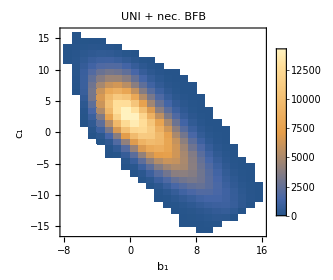
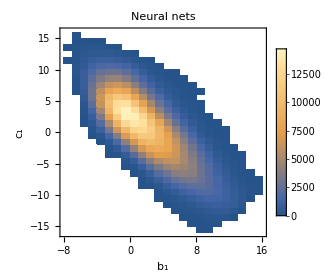
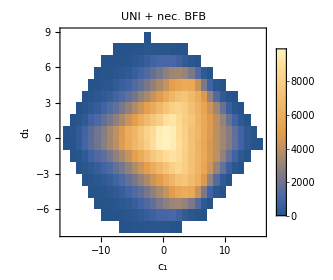
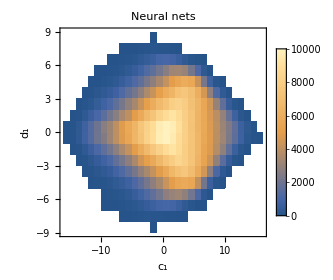
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
parNames={"a_1","a_2","a_3","b_1","b_2","b_3","c_1","c_2","c_3","d_1","d_2","d_3"};
Table[{Show[{DensityHistogram[validParamSet[[;;,xx]],ChartLegends->Automatic,PerformanceGoal->"Quality",PlotLabel->"UNI + nec. BFB"],ConvexHullMesh[validParamSet[[;;,xx]],MeshCellStyle->{1->{Green},2->Opacity[0]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->280,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}],Show[{DensityHistogram[validParamNets[[;;,xx]],ChartLegends->Automatic,PerformanceGoal->"Quality",PlotLabel->"Neural nets"],ConvexHullMesh[validParamNets[[;;,xx]],MeshCellStyle->{1->{Red},2->Opacity[0]}]},PlotRange->Automatic,Frame->True,AspectRatio->1,FrameStyle->Black,ImageSize->280,FrameLabel->{Style[parNames⟦xx[[1]]⟧,16,Black],Style[parNames⟦xx[[2]]⟧,16,Black]}]},{xx,{{4,7},{7,10}}}];
Grid[%]
```

#### Import & Export Data

Because many data formats are possible, we allow users to import the data into Mathematica themselves. The imported data can then be passed to wbBrancUniBFBcheck by setting the global parameter wbParamData.

```mathematica
initFile=Import[ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/Data/initial_set.csv"];
```

```mathematica
wbParamData=initFile;
{initParamSet,dataNec3}=wbBrancUniBFBcheck[3,"GeneratePoints"->False];
```

Run time of the BFB enforcement (mode 3): 0.177081 sec.

BFB points: 759

Alternatively, the imported data can be passed directly to wbBrancUniBFBcheck (note that the option "GeneratePoints" → False can be omitted):

```mathematica
{initParamSet,dataNec3}=wbBrancUniBFBcheck[initFile,3];
```

Run time of the BFB enforcement (mode 3): 0.180874 sec.

BFB points: 759

By setting "ExportData" → True, an initial and validated data sets are exported to the folder “Data”, with file names specified by the "FileNameInit" and "FileNameValid" options:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[2,"ExportData"->True,"FileNameInit"->"init1.csv","FileNameValid"->"valid1.csv"];
```

Run time of data generation (UNI+Nec1): 0.455599 sec.

Run time of the BFB enforcement (mode 2): 0.067174 sec.

BFB points: 735

#### ShowMessages

The status of intermediate computations is displayed at the bottom of the evaluation notebook. In addition, messages reporting computation times and results are printed at the end of each step.

By setting "ShowMessages" → False, messages reporting computation times and results are suppressed. This is convenient when wbBrancUniBFBcheck is used inside loops or similar workflows:

```mathematica
{initParamSet,dataUNI}=wbBrancUniBFBcheck[1,"NPoints"->10^5,"ImposeBFB"->False];
wbParamData=dataUNI;
```

Run time of data generation (UNI): 3.04517 sec.

```mathematica
Table[mode->Length@Last@wbBrancUniBFBcheck[mode,"GeneratePoints"->False,"ShowMessages"->False],{mode,1,4}]
```

{1→228,2→178,3→177,4→177}

#### NPoints

The "NPoints" → n option sets the number of points generated in the initial data set; however, the validated data set may contain fewer points:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[2,"NPoints"->10^4];
Length/@{initParamSet,validParamSet}
```

Run time of data generation (UNI+Nec1): 4.0326 sec.

Run time of the BFB enforcement (mode 2): 0.228143 sec.

BFB points: 7531

{10000,7531}

#### MaxCoupling

The "MaxCoupling" → n_max option sets the bounds for the generated couplings such that |coupling| ≤ n_max:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[1,"MaxCoupling"->20,"ImposeUNI"->False];
MinMax/@Transpose@initParamSet
```

Run time of data generation (Nec1): 0.04425 sec.

{{0.10721,19.9693},{0.0870998,19.9839},{0.00416046,19.9724},{-16.8813,19.9897},{-17.4378,19.9726},{-16.1146,19.987},{-19.9889,19.9986},{-19.7722,19.9835},{-19.9812,19.9551},{-19.8963,19.9294},{-19.9705,19.9481},{-19.9858,19.9318}}

#### BoundUNI

The "BoundUNI" → M_max option sets the unitarity bound, i.e. the eigenvalues of the scattering matrix are required to be bounded by a quantity M_max, which is typically taken to be 8π. In some cases, a relaxed unitarity bound may be used:

```mathematica
{initParamSet,validParamSet}=wbBrancUniBFBcheck[1,"MaxCoupling"->35,"BoundUNI"->16 π,"ImposeBFB"->False];
MinMax/@Transpose@initParamSet
```

Run time of data generation (UNI): 2.10187 sec.

{{-16.7263,16.4385},{-16.4756,16.1851},{-16.1588,16.3355},{-29.0682,29.6806},{-28.172,29.7631},{-29.2432,29.4411},{-30.3202,30.4447},{-31.5754,29.9483},{-31.3193,31.3246},{-16.1095,15.9213},{-15.7467,16.3574},{-15.9001,16.2963}}

## Source & Additional Information

### Related Symbols

wbBrancParRnd ▪ wbBrancParRndNec ▪ wbBrancParRndUni ▪ wbBrancParRndUniNec ▪ wbBrancUNICond ▪ wbBrancUNINec1Cond ▪ wbBrancSufCond  ▪ wbBrancNecCond1  ▪ wbBrancNecCond2  ▪ wbBrancNecCond3 ▪ wbMinimFuncPotBranc ▪ wbWeinUniBFBcheck

### References

[1] D. Jurčiukonis, L. Lavoura and A. Milagre, Algorithm and AI for finding out whether the scalar potential of a three-Higgs-doublet model with Z_2 x Z_2 symmetry is bounded from below, arXiv:26xx.xxxxx [hep-ph].